## Problem I-B: Padé approximants of orders [2,3] and [4,1]

### For the coefficients of P[2,3]:

```mathematica
coeff1=Solve[{b1+1==a1,2b2+2b1+1==2a2,6b3+6b2+3b1+1==0,24b3+12b2+4b1+1==0,60b3+20b2+5b1+1==0},{a1,a2,b1,b2,b3},Reals]
```

{{a1→2/5,a2→1/20,b1→-3/5,b2→3/20,b3→-1/60}}

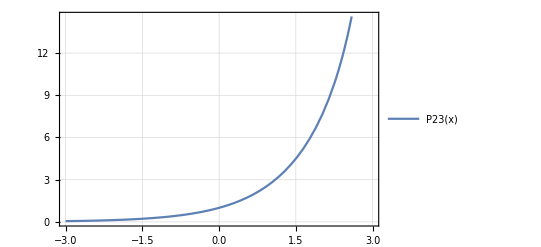

```mathematica
a11=a1/.coeff1[[1]];
a21=a2/.coeff1[[1]];
b11=b1/.coeff1[[1]];
b21=b2/.coeff1[[1]];
b31=b3/.coeff1[[1]];
P23[x_]:=(1+a11*x+a21*x^2)/(1+b11*x+b21*x^2+b31*x^3)
plot1=Plot[P23[x],{x,-3,3},PlotTheme->"Detailed"]
```

### For P[4,1]:

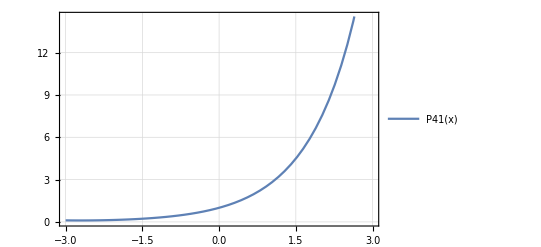

```mathematica
P41[x_]:=(1+4x/5 +3x^2 /10 +x^3 /15 + x^4 /120)/(1-x/5)
plot2=Plot[P41[x],{x,-3,3},PlotTheme->"Detailed"]
```

### Comparison

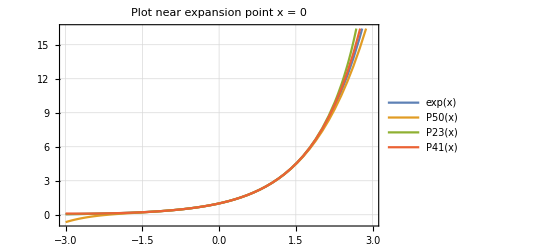

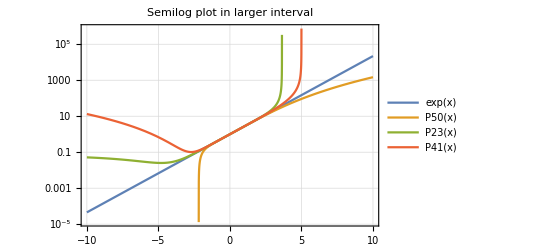

```mathematica
P50[x_]:=Sum[x^n / Factorial[n],{n,0,5}]
Plot[{Exp[x],P50[x],P23[x],P41[x]},{x,-3,3},PlotTheme->"Detailed",PlotLabel->"Plot near expansion point x = 0"]
LogPlot[{Exp[x],P50[x],P23[x],P41[x]},{x,-10,10},PlotTheme->"Detailed",PlotLabel->"Semilog plot in larger interval"]
```

### Some values...

```mathematica
Exp[0.5]
```

1.64872

```mathematica
P50[0.5]
```

1.6487

```mathematica
P23[0.5]
```

1.64873

```mathematica
P41[0.5]
```

1.64873

```mathematica
Exp[1]//N
```

2.71828

```mathematica
P50[1]//N
```

2.71667

```mathematica
P23[1]//N
```

2.71875

```mathematica
P41[1]//N
```

2.71875

```mathematica
Exp[2]//N
```

7.38906

```mathematica
P50[2]//N
```

7.26667

```mathematica
P23[2]//N
```

7.5

```mathematica
P41[2]//N
```

7.44444

```mathematica
Exp[5]//N
```

148.413

```mathematica
P50[5]//N
```

91.4167

```mathematica
P23[5]//N
```

-12.75

```mathematica
P41[5]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity